## Numerical Fit Data

```mathematica
data=Import["/home/pratul/Downloads/Project/Analytical fits/New results/Best_dataset.txt","Table"]
```

{{#,hybrid,q,eta,tshift,tmatch_amp,tmatch_freq,l0,e0},{1.,1355,1.,0.25,-60.,-61.131,-1270.26,1.423,0.173},{2.,1356,1.,0.25,35.,-30.2792,-3369.34,1.574,0.23},{3.,1358,1.,0.25,-50.,-50.8727,-545.853,-2.682,0.322},{4.,1359,1.,0.25,-75.,-75.9144,-931.066,1.834,0.317},{5.,1360,1.,0.25,85.,-50.2038,-2168.94,-0.395,0.416},{6.,1361,1.,0.25,90.,-55.0928,-2012.11,-1.019,0.416},{7.,1364,2.,0.22222,0.,-30.1312,-4376.08,-0.181,0.172},{8.,1365,2.,0.22222,85.,-125.074,-3448.13,-1.127,0.209},{9.,1366,2.,0.22222,45.,-30.3449,-2467.68,-2.89,0.32},{10.,1367,2.,0.22222,-60.,-61.2333,-1583.98,1.687,0.32},{11.,1368,2.,0.22222,35.,-29.8486,-2900.13,0.42,0.324},{12.,1372,3.,0.1875,-35.,-35.933,-2207.17,3.005,0.3},{13.,1373,3.,0.1875,105.,-29.9458,-2654.06,1.682,0.3}}

```mathematica
sn=Flatten[data[[2;;,1;;1]]]
simVec=Flatten[data[[2;;,2;;2]]]
qVec=Flatten[data[[2;;,3;;3]]]
etaVec=Flatten[data[[2;;,4;;4]]]
tshiftVec=Flatten[data[[2;;,5;;5]]]
tmatch$ampVec=Flatten[data[[2;;,6;;6]]]
tmatch$freqVec=Flatten[data[[2;;,7;;7]]]
l0Vec=Flatten[data[[2;;,8;;8]]]
e0Vec=Flatten[data[[2;;,9;;9]]]
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.}

{1355,1356,1358,1359,1360,1361,1364,1365,1366,1367,1368,1372,1373}

{1.,1.,1.,1.,1.,1.,2.,2.,2.,2.,2.,3.,3.}

{0.25,0.25,0.25,0.25,0.25,0.25,0.22222,0.22222,0.22222,0.22222,0.22222,0.1875,0.1875}

{-60.,35.,-50.,-75.,85.,90.,0.,85.,45.,-60.,35.,-35.,105.}

{-61.131,-30.2792,-50.8727,-75.9144,-50.2038,-55.0928,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-35.933,-29.9458}

{-1270.26,-3369.34,-545.853,-931.066,-2168.94,-2012.11,-4376.08,-3448.13,-2467.68,-1583.98,-2900.13,-2207.17,-2654.06}

{1.423,1.574,-2.682,1.834,-0.395,-1.019,-0.181,-1.127,-2.89,1.687,0.42,3.005,1.682}

{0.173,0.23,0.322,0.317,0.416,0.416,0.172,0.209,0.32,0.32,0.324,0.3,0.3}

## Model Fits (based on sets with unique eccentricity)

### (Hinder+ inspired) Frequency (t_match model)

```mathematica
(*selects fits within 200M of the merger*)
```

```mathematica
simlist={1355,1356,1358,1359,1360,1361,1364,1365,1366,1367,1368,1372,1373};
simlist=simVec;
idxlist ={};
For[k=1,k<14,k++,If[simVec[[k]]==simlist[[k]], AppendTo[idxlist,k]]]
idxlist
```

{1,2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
Length[idxlist]
```

13

```mathematica
etaVec=etaVec[[idxlist]];
qVec=qVec[[idxlist]];
e0Vec=e0Vec[[idxlist]];
l0Vec=l0Vec[[idxlist]];
tmatch$freqVec=tmatch$freqVec[[idxlist]];
tmatch$ampVec=tmatch$ampVec[[idxlist]];
tshiftVec=tshiftVec[[idxlist]];
```

```mathematica
numfit=Table[{etaVec[[i]],e0Vec[[i]],l0Vec[[i]],tmatch$freqVec[[i]]},{i,1,Length[etaVec]}]
```

{{0.25,0.173,1.423,-1270.26},{0.25,0.23,1.574,-3369.34},{0.25,0.322,-2.682,-545.853},{0.25,0.317,1.834,-931.066},{0.25,0.416,-0.395,-2168.94},{0.25,0.416,-1.019,-2012.11},{0.22222,0.172,-0.181,-4376.08},{0.22222,0.209,-1.127,-3448.13},{0.22222,0.32,-2.89,-2467.68},{0.22222,0.32,1.687,-1583.98},{0.22222,0.324,0.42,-2900.13},{0.1875,0.3,3.005,-2207.17},{0.1875,0.3,1.682,-2654.06}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*η+a2*η^2+b1*e+b2*e^2+b3*e^3+c1 e η+c2 e^2 η+c3*e*η^2+c4*e^2*η^2+c5*e^3*η(*+c6*e^3*η^2*)+d1 e η Cos[l+d2]+d3 e^2 η^2 Cos[l+d4]+d5 e^3 η Cos[e l+d6]+d7 e^3 η^2 Cos[e l+d8]},{a0,a1,a2,b1,b2,b3,c1,c2,c3,c4,c5,(*c6,*) d1,d2,d3,d4, d5, d6,d7, d8},{η,e,l},MaxIterations->10000]
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a0→-27718.5,a1→101137.,a2→648187.,b1→-74161.4,b2→1.27927×10^6,b3→-1.58239×10^6,c1→-1.17665×10^6,c2→-304352.,c3→-371850.,c4→-160890.,c5→-646066.,d1→83930.4,d2→1226.38,d3→-1.61714×10^6,d4→-1048.81,d5→-3.06827×10^6,d6→-851.527,d7→1.41757×10^6,d8→-2348.24}

```mathematica
(*NOTE. circular cubic eta terms may not be useful due to low mass ratio cases under consideration*)
```

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]+d7 ee^3 ηη^2 Cos[ee ll+d8]/.{ηη->etaVec,ee->e0Vec,ll->l0Vec}/.FitFunc
```

{-1270.26,-3369.34,-545.853,-931.066,-2168.94,-2012.11,-4376.08,-3448.13,-2467.68,-1583.98,-2900.13,-2207.17,-2654.06}

```mathematica
res=tmatch$freqVec-model
Max[Abs[res]]
Mean[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{2.04636×10^-12,3.13776×10^-10,-5.65024×10^-11,2.89219×10^-10,4.00178×10^-11,-2.23054×10^-10,-1.4461×10^-10,8.73115×10^-11,-6.08452×10^-10,4.79758×10^-11,-1.00044×10^-10,5.9481×10^-10,1.12777×10^-10}

6.08452×10^-10

2.01584×10^-10

{1.12777×10^-10,2.89219×10^-10,5.9481×10^-10,6.08452×10^-10}

1.01423×10^-18

```mathematica
(*75% simulations have fits within 30M.. *)
```

```mathematica
(*snum={};For[i=1,i<21,i++,snum=AppendTo[snum,ToString[i]]]*)
```

```mathematica
tmatch$freqVec
```

{-1270.26,-3369.34,-545.853,-931.066,-2168.94,-2012.11,-4376.08,-3448.13,-2467.68,-1583.98,-2900.13,-2207.17,-2654.06}

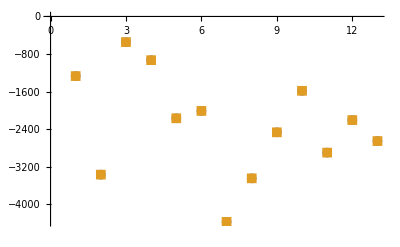

```mathematica
ListPlot[{tmatch$freqVec,model},PlotMarkers->{Automatic,10
}]
```

```mathematica
fitrule$tmatch$freq=FitFunc
```

{a0→-27718.5,a1→101137.,a2→648187.,b1→-74161.4,b2→1.27927×10^6,b3→-1.58239×10^6,c1→-1.17665×10^6,c2→-304352.,c3→-371850.,c4→-160890.,c5→-646066.,d1→83930.4,d2→1226.38,d3→-1.61714×10^6,d4→-1048.81,d5→-3.06827×10^6,d6→-851.527,d7→1.41757×10^6,d8→-2348.24}

### TEST (freq model)

Model should produce a negative t_match for values for (e_ 0 , q, l_ 0) in the calibration range or at least the range of values the model is expected to work well. We choose this range as e_ 0 (0.01 - 0.2), q (1 - 3) and l_ 0 (-π, π).

```mathematica
e0testVec=Table[e0,{e0,0.1,0.2,0.000001}];
qtestVec=Range[1,3,0.00001];
etatestVec=qtestVec/(1+qtestVec)^2;
l0testVec=N[Range[-π,π,π/100000]];
```

```mathematica
Length[e0testVec]
```

100001

```mathematica
Length[qtestVec]
```

200001

```mathematica
Length[l0testVec]
```

200001

```mathematica
e0testVecNew=e0testVec[[SeedRandom[1234];RandomInteger[{1,Length[e0testVec]},10000]]];
```

```mathematica
qtestVecNew = qtestVec[[SeedRandom[1234];RandomInteger[{1,Length[etatestVec]},10000]]];
```

```mathematica
etafromq = qtestVecNew/(1+qtestVecNew)^2;
```

```mathematica
etatestVecNew=etatestVec[[SeedRandom[1234];RandomInteger[{1,Length[etatestVec]},10000]]];
```

```mathematica
l0testVecNew=l0testVec[[SeedRandom[1234];RandomInteger[{1,Length[l0testVec]},10000]]];
```

```mathematica
e0testVecNew;
```

```mathematica
qtestVecNew;
```

```mathematica
etafromq -etatestVecNew;
```

```mathematica
etatestVecNew;
```

```mathematica
l0testVecNew;
```

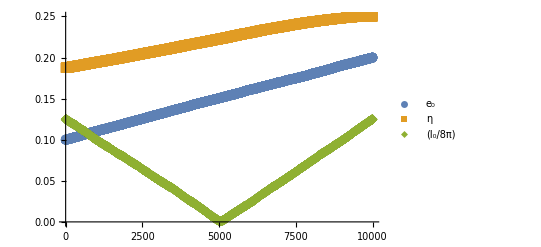

```mathematica
ListPlot[{Sort[e0testVecNew],Sort[etatestVecNew],Abs[Sort[l0testVecNew]]/(8π)},PlotMarkers->{Automatic,10},PlotLegends->{"e_0","η","(l_0/8π)"}]
```

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]+d7 ee^3 ηη^2 Cos[ee ll+d8]/.{ηη->etatestVecNew,ee->e0testVecNew,ll->l0testVecNew}/.FitFunc;
```

```mathematica
testidxlist ={};
For[k=1,k<10001,k++,If[model[[k]]>0, AppendTo[testidxlist,k]]]
testidxlist;
```

```mathematica
e0testVecNew[[testidxlist]];
```

```mathematica
qtestVecNew[[testidxlist]];
```

```mathematica
etafromq[[testidxlist]]-etatestVecNew[[testidxlist]];
```

```mathematica
etatestVecNew[[testidxlist]];
```

```mathematica
l0testVecNew[[testidxlist]];
```

```mathematica
Length[testidxlist]
```

3870

```mathematica
testidxlist2={};
For[k=1,k<10001,k++,If[model[[k]]<0, AppendTo[testidxlist2,k]]]
testidxlist2;
```

```mathematica
Length[testidxlist2]
```

6130

### (Hinder+ inspired) Amplitude (t_match model)

```mathematica
numfit=Table[{etaVec[[i]],e0Vec[[i]],l0Vec[[i]],tmatch$ampVec[[i]]},{i,1,Length[etaVec]}]
```

{{0.25,0.173,1.423,-61.131},{0.25,0.23,1.574,-30.2792},{0.25,0.322,-2.682,-50.8727},{0.25,0.317,1.834,-75.9144},{0.25,0.416,-0.395,-50.2038},{0.25,0.416,-1.019,-55.0928},{0.22222,0.172,-0.181,-30.1312},{0.22222,0.209,-1.127,-125.074},{0.22222,0.32,-2.89,-30.3449},{0.22222,0.32,1.687,-61.2333},{0.22222,0.324,0.42,-29.8486},{0.1875,0.3,3.005,-35.933},{0.1875,0.3,1.682,-29.9458}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*η+a2*η^2+b1*e+b2*e^2+b3*e^3+c1 e η+c2 e^2 η+c3*e*η^2+c4*e^2*η^2+c5*e^3*η(*+c6*e^3*η^2*)+d1 e η Cos[l+d2]+d3 e^2 η^2 Cos[l+d4]+d5 e^3 η Cos[e l+d6]},{a0,a1,a2,b1,b2,b3,c1,c2,c3,c4,c5(*,c6*),d1,d2,d3,d4,d5,d6},{η,e,l},MaxIterations->10000]
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a0→5181.52,a1→-8713.31,a2→-28516.9,b1→-38189.8,b2→83382.,b3→-95039.5,c1→67853.2,c2→17460.5,c3→26929.3,c4→1443.14,c5→-38609.5,d1→-8409.99,d2→7.08161,d3→130405.,d4→-87.3613,d5→-79003.1,d6→6.20544}

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]/.{ηη->etaVec,ee->e0Vec,ll->l0Vec}/.FitFunc
```

{-61.131,-30.2792,-50.8727,-75.9144,-50.2038,-55.0928,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-35.933,-29.9458}

```mathematica
res=tmatch$ampVec-model
Max[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{-1.37845×10^-12,3.55271×10^-15,1.42109×10^-12,-1.16529×10^-12,-3.19744×10^-12,-8.10019×10^-13,-5.40012×10^-13,-1.13687×10^-12,7.10543×10^-15,-1.39977×10^-12,-5.3646×10^-13,7.53175×10^-13,-1.06581×10^-12}

3.19744×10^-12

{1.06581×10^-12,1.37845×10^-12,1.42109×10^-12,3.19744×10^-12}

2.16918×10^-23

```mathematica
(*90% of fits (18) have res better than 10M*)
```

```mathematica
fitrule$tmatch$amp=FitFunc
```

{a0→5181.52,a1→-8713.31,a2→-28516.9,b1→-38189.8,b2→83382.,b3→-95039.5,c1→67853.2,c2→17460.5,c3→26929.3,c4→1443.14,c5→-38609.5,d1→-8409.99,d2→7.08161,d3→130405.,d4→-87.3613,d5→-79003.1,d6→6.20544}

```mathematica
tmatch$ampVec
```

{-61.131,-30.2792,-50.8727,-75.9144,-50.2038,-55.0928,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-35.933,-29.9458}

```mathematica
model
```

{-61.131,-30.2792,-50.8727,-75.9144,-50.2038,-55.0928,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-35.933,-29.9458}

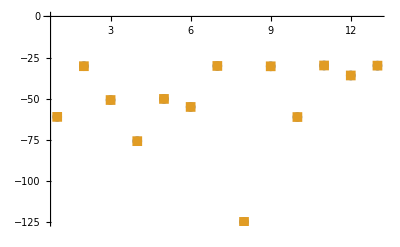

```mathematica
ListPlot[{tmatch$ampVec,model},PlotMarkers->{Automatic,10},PlotRange->All]
```

### TEST (amp model)

Model should produce a negative t_match for values for (e_ 0 , q, l_ 0) in the calibration range or at least the range of values the model is expected to work well. We choose this range as e_ 0 (0.01 - 0.2), q (1 - 3) and l_ 0 (-π,  π).

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]/.{ηη->etatestVecNew,ee->e0testVecNew,ll->l0testVecNew}/.FitFunc;
```

```mathematica
testidxlist3={};
For[k=1,k<10001,k++,If[model[[k]]>0, AppendTo[testidxlist3,k]]]
testidxlist3;
```

```mathematica
Length[testidxlist3]
```

5824

```mathematica
testidxlist4={};
For[k=1,k<10001,k++,If[model[[k]]<0, AppendTo[testidxlist4,k]]]
testidxlist4;
```

```mathematica
Length[testidxlist4]
```

4176

```mathematica
idxlistformismatch=Intersection[testidxlist2,testidxlist4];
```

```mathematica
Length[idxlistformismatch]
```

1157

```mathematica
Sort[e0testVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[qtestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[etafromq[[idxlistformismatch]]];
```

```mathematica
Sort[etatestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[etafromq[[idxlistformismatch]]]-Sort[etatestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[l0testVecNew[[idxlistformismatch]]];
```

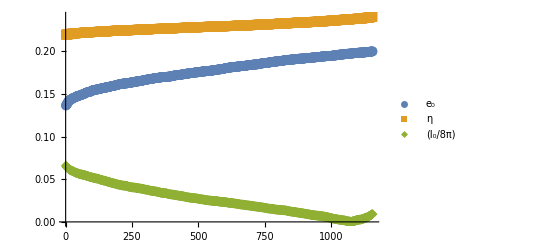

```mathematica
ListPlot[{Sort[e0testVecNew[[idxlistformismatch]]],Sort[etatestVecNew[[idxlistformismatch]]],Abs[Sort[l0testVecNew[[idxlistformismatch]]]]/(8π)},PlotMarkers->{Automatic,10},PlotLegends->{"e_0","η","(l_0/8π)"}]
```

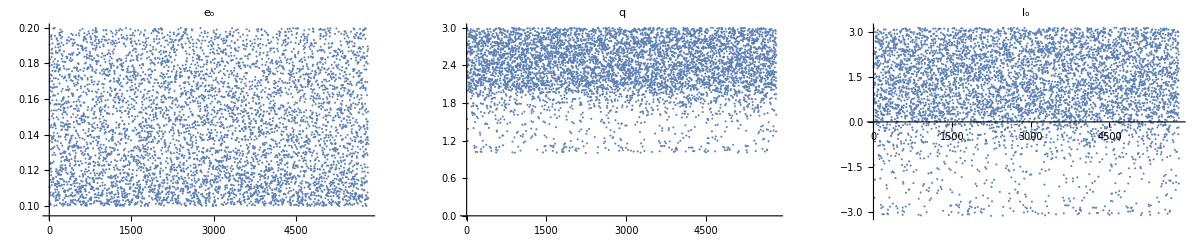

```mathematica
p1=ListPlot[e0testVecNew[[testidxlist3]],PlotLabel->"e_o"];
p2=ListPlot[qtestVecNew[[testidxlist3]],PlotLabel->"q"];
p3 = ListPlot[l0testVecNew[[testidxlist3]],PlotLabel->"l_o"];
GraphicsRow[{p1,p2,p3},ImageSize->Full]
```

```mathematica
e0testVecNew[[idxlistformismatch]]; (* use these values for e0 *)
```

```mathematica
qtestVecNew[[idxlistformismatch]]; (* use these values for q *)
```

```mathematica
etatestVecNew[[idxlistformismatch]]; (* use these values for eta *)
```

```mathematica
l0testVecNew[[idxlistformismatch]] ;(* use these values for l0 *)
```

```mathematica
etafromq[[idxlistformismatch]]-etatestVecNew[[idxlistformismatch]];
```

```mathematica
(*dat1=Flatten/@Transpose[{qtestVecNew[[idxlistformismatch]],etatestVecNew[[idxlistformismatch]],e0testVecNew[[idxlistformismatch]],l0testVecNew[[idxlistformismatch]]}];
Export["physical_data_10kpts.txt",dat1,"Table"]*)
```

### (Hinder+ inspired) t-shift (e, q, l) model

```mathematica
numfit=Table[{qVec[[i]],e0Vec[[i]],l0Vec[[i]],tshiftVec[[i]]},{i,1,Length[etaVec]}]
```

{{1.,0.173,1.423,-60.},{1.,0.23,1.574,35.},{1.,0.322,-2.682,-50.},{1.,0.317,1.834,-75.},{1.,0.416,-0.395,85.},{1.,0.416,-1.019,90.},{2.,0.172,-0.181,0.},{2.,0.209,-1.127,85.},{2.,0.32,-2.89,45.},{2.,0.32,1.687,-60.},{2.,0.324,0.42,35.},{3.,0.3,3.005,-35.},{3.,0.3,1.682,105.}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*q+a2*q^2+b1*e+b2*e^2+b3*e^3+c1 e q+c2 e^2 q+c3*e*q^2+c4*e^2*q^2+c5*e^3*q(*+c6*e^3*q^2*)+d1 e q Cos[l+d2]+d3 e^2 q^2 Cos[e l+d4]+d5 e^3 q Cos[l+d6]+d7 e q^2 Cos[l+d8]},{a0,a1,a2,b1,b2,b3,c1,c2,c3, c4,c5,(*c6,*)d1,d2,d3,d4,d5,d6,d7,d8},{q,e,l},MaxIterations->1000]
```

{a0→-739.225,a1→-60.6414,a2→-142.463,b1→3014.06,b2→-3084.44,b3→-2738.73,c1→2570.28,c2→-3442.23,c3→1251.02,c4→-4287.32,c5→-2912.1,d1→464.638,d2→-0.248561,d3→924.196,d4→0.418974,d5→5462.63,d6→-17.8465,d7→409.651,d8→-2.68893}

```mathematica
model=a0+a1*qq+a2*qq^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*qq+c2*ee^2*qq+c3*ee*qq^2+c4*ee^2*qq^2+c5*ee^3*qq(*+c6*ee^3*qq^2*)+d1 ee qq Cos[ll+d2]+d3 ee^2 qq^2 Cos[ee ll+d4]+d5 ee^3 qq Cos[ll+d6]+d7 ee qq^2 Cos[ll+d8]/.FitFunc/.{qq->qVec,ee->e0Vec,ll->l0Vec}
```

{-60.,35.,-50.,-75.,85.,90.,5.11591×10^-13,85.,45.,-60.,35.,-35.,105.}

```mathematica
res=Abs[tshiftVec-model]
Max[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{2.41585×10^-13,2.77112×10^-13,7.38964×10^-13,5.11591×10^-13,1.25056×10^-12,5.68434×10^-13,5.11591×10^-13,9.66338×10^-13,8.52651×10^-13,2.84217×10^-13,4.54747×10^-13,1.25056×10^-12,1.93268×10^-12}

1.93268×10^-12

{5.68434×10^-13,9.66338×10^-13,1.25056×10^-12,1.93268×10^-12}

1.03392×10^-23

```mathematica
(*95% of fits have res better than 10M*)
```

```mathematica
fitrule$tshift=FitFunc
```

{a0→-739.225,a1→-60.6414,a2→-142.463,b1→3014.06,b2→-3084.44,b3→-2738.73,c1→2570.28,c2→-3442.23,c3→1251.02,c4→-4287.32,c5→-2912.1,d1→464.638,d2→-0.248561,d3→924.196,d4→0.418974,d5→5462.63,d6→-17.8465,d7→409.651,d8→-2.68893}

```mathematica
e0Vec
```

{0.173,0.23,0.322,0.317,0.416,0.416,0.172,0.209,0.32,0.32,0.324,0.3,0.3}

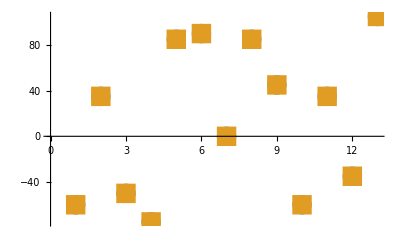

```mathematica
ListPlot[{tshiftVec,model},PlotMarkers->{Automatic,20}]
```